```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
```

```mathematica
β0 =8.;
```

```mathematica
bubble = ReadList[NotebookDirectory[]<>"Bbeta"<>ToString[NumberForm[β0,{3,2}]]<>"j0.dat",Table[Number,{4}]];
bubble[[All,3]] = bubble[[All,3]]*bubble[[All,4]];
```

```mathematica
bounds = {Min@#,Max@#}&@bubble[[All,3]];
invmollweide[{x_,y_}]:=With[{theta=ArcSin[y]},{Pi x/(2 Cos[theta]),ArcSin[(2 theta+Sin[2 theta])/Pi]}]
Legended[ImageTransformation[ListDensityPlot[Join[{Mod[#[[2]],2Pi]-Pi,#[[1]]+Pi/2,#[[3]]}&/@bubble,{Mod[#[[2]],2Pi]-Pi,#[[1]]-3Pi/2,#[[3]]}&/@bubble,{Mod[#[[2]],2Pi]-Pi,#[[1]]-Pi/2,#[[3]]}&/@bubble],PlotRange->{{-Pi,Pi},{-Pi/2,Pi/2},All},PlotRangePadding->None,Frame->None,ImagePadding->None,ColorFunction->"Rainbow",AspectRatio->1/2,ImageSize->600],invmollweide,DataRange->{{-Pi,Pi},{-Pi/2,Pi/2}},PlotRange->{{-2,2},{-1,1}},Masking->All,Background->White],BarLegend[{"Rainbow",bounds},LegendLabel->Style["βa_cR_c",Black,14],LegendMarkerSize->160,LabelStyle->{Black,FontSize-> 12,FontFamily->"Times"}]]
```

-Graphics-

```mathematica
Ωlist = Table[ReadList[NotebookDirectory[]<>"OmegaGWbeta"<>ToString[NumberForm[β0,{3,2}]]<>"j"<>ToString@index<>".dat",Table[Number,3]],{index,{0,1,2,3}}];
LLΩk = {Interpolation[Log10@{#[[1]],#[[2]]}&/@Mean@Ωlist,InterpolationOrder->1],Interpolation[Log10@{#[[1]],#[[3]]}&/@Mean@Ωlist,InterpolationOrder->1]};
```

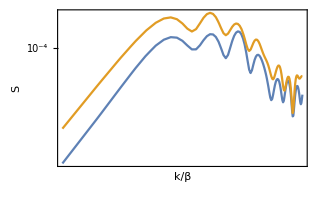

```mathematica
Plot[{LLΩk[[1]][x],LLΩk[[2]][x]},{x,LLΩk[[1,1,1,1]],LLΩk[[1,1,1,2]]},FrameLabel->{"k/β","S"},ImageSize->{320,Automatic},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}}]
```

```mathematica
ρlist = Table[ReadList[NotebookDirectory[]<>"OmegaTotGWbeta"<>ToString[NumberForm[β0,{3,2}]]<>"j"<>ToString@index<>".dat",Table[Number,4]],{index,{0,1,2,3}}];
ρt = Table[{Interpolation[{#[[1]],#[[3]]}&/@ρlist[[j]],InterpolationOrder->1],Interpolation[{#[[1]],#[[4]]}&/@ρlist[[j]],InterpolationOrder->1]},{j,Length@ρlist}];
```

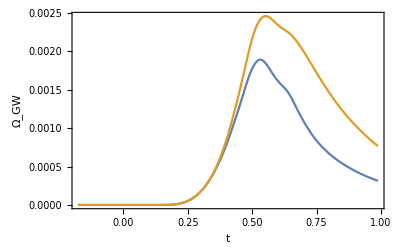

```mathematica
Plot[#[t]&/@Flatten[ρt]//Evaluate,{t,ρt[[1,1,1,1,1]],ρt[[1,1,1,1,2]]},FrameLabel->{"t","Ω_GW"}]
```